## Definitions

```mathematica
PM={IdentityMatrix[2],PauliMatrix[1],PauliMatrix[2],PauliMatrix[3]};
X[μ_]:=PM⟦μ+1⟧
X[μ_,ν_]:=KroneckerProduct[PM⟦μ+1⟧,PM⟦ν+1⟧]
```

## Hamiltonian

```mathematica
T=I X[0,2]; C2=I X[0,3];
```

```mathematica
MatAllowed=Table[(Norm[T.Conjugate[X[i,j].Inverse[T]]-X[i,j]]+Norm[C2.X[i,j].Inverse[C2]-X[i,j]]),{i,0,3},{j,0,3}];
HBulkAddition=0.5 Sum[Which[MatAllowed[[a+1,b+1]]==0,(RandomReal[0.5]-0.25)X[a,b],True,ConstantArray[0,{4,4}]],{a,0,3},{b,0,3}];
```

```mathematica
H[k_]:=Cos[k]X[3,0]+Sin[k]X[1,1]+.5HBulkAddition
```

```mathematica
Norm[T.Conjugate[H[1.]].Inverse[T]-H[-1.]]+Norm[C2.H[1.].Inverse[C2]-H[-1.]]+Norm[T.Conjugate[C2].Inverse[T]-C2]
```

0.

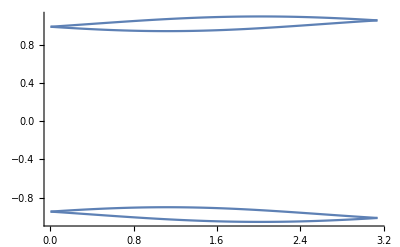

```mathematica
Plot[Sort[Eigenvalues[N[H[k]]]],{k,0,Pi},PlotRange->All,GridLines->{{0,Pi/2,Pi},{}}]
```

## Gauge Invariant Wilson Loop

```mathematica
eigsysloc[k_] := Orthogonalize[Block[{es=Eigensystem[N@H[k]]},es⟦2,Ordering[Re[es⟦1⟧]]⟧]];
```

```mathematica
Proj[k_]:=Sum[Outer[Times,eigsysloc[k][[i]],Conjugate[eigsysloc[k][[i]]]],{i,2}]
```

```mathematica
W=Dot@@ParallelTable[Proj[k],{k,0,2Pi,2Pi/1024}];
```

```mathematica
Eigenvalues@W
```

{-0.995178,-0.995178,4.8782×10^-17,2.0657×10^-18}

## Parallel Transport for Smooth Gauge

```mathematica
n=2000;
```

```mathematica
δ=2Pi/n;
```

```mathematica
eigsysloc[k_] := Orthogonalize[Block[{es=Eigensystem[N@H[k]]},es⟦2,Ordering[Re[es⟦1⟧]]⟧]];
```

```mathematica
utilde=ParallelTable[Orthogonalize[eigsysloc[k]⟦1;;2⟧],{k,0,2Pi,δ}];
```

```mathematica
u={utilde⟦1⟧};
For[i=2,i≤n+1,i++,
Ltilde=Conjugate[u⟦i-1⟧].Transpose[utilde⟦i⟧];
{V,Σ,W}=SingularValueDecomposition[Ltilde];
U=W.ConjugateTranspose[V];
AppendTo[u,Transpose[U].(utilde⟦i⟧)];
];
Λ=Conjugate[u⟦n+1⟧].Transpose[u⟦1⟧];
{ϕ,S}={Eigensystem[Λ]⟦1⟧,Orthogonalize[Eigensystem[Λ]⟦2⟧]};
urotated=Table[S.el,{el,u}];
ufinal=Table[Table[urotated⟦index,index2⟧Exp[Log[ϕ⟦index2⟧](index-1)/n],{index2,Length[urotated[[index]]]}],{index,Length[urotated]}];
```

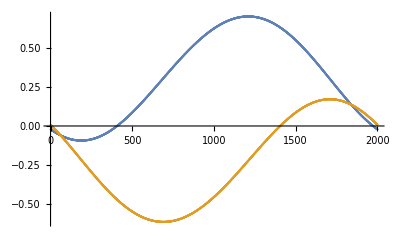

```mathematica
ListPlot[Transpose@ReIm@ufinal[[All,1,1]],PlotRange->All]
```

```mathematica
W=Dot@@ParallelTable[Transpose[ufinal[[i]]].Conjugate[ufinal[[i]]],{i,1,n}];
```

```mathematica
Eigenvalues[W]//Chop
```

{-0.997528,-0.997528,0,0}